# Constructing Zika suitability predictor

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Dropbox/current-projects/zika-usvi/zika-suitability

## GeoTIFF import

```mathematica
Import[ "zikamask2502.tif",{"GeoTIFF","Elements"}]
```

{Centering,CentralScaleFactor,ColorSpace,CoordinateSystem,CoordinateSystemInformation,Data,DataFormat,Datum,ElevationRange,Graphics,GridOrigin,Image,InverseFlattening,LinearUnits,Projection,ProjectionName,RasterSize,ReferenceModel,SemimajorAxis,SemiminorAxis,SpatialRange,SpatialResolution,StandardParallels}

```mathematica
Import["zikamask2502.tif",{"GeoTIFF","Projection"}]
```

{None,ReferenceModel→{6.35675×10^6 m,6.37814×10^6 m}}

```mathematica
Import["zikamask2502.tif",{"GeoTIFF","SpatialRange"}]
```

{{-60. °,84.9999 °},{-180. °,180. °}}

```mathematica
Import["zikamask2502.tif",{"GeoTIFF","CoordinateSystemInformation"}]
```

GEOGCS→{WGS 84,DATUM→{WGS_1984,SPHEROID→{WGS 84,6378137,298.257,AUTHORITY→{EPSG,7030}},AUTHORITY→{EPSG,6326}},PRIMEM→{Greenwich,0},UNIT→{degree,0.0174533},AUTHORITY→{EPSG,4326}}

```mathematica
geo=Import["zikamask2502.tif",{"GeoTIFF","Data"}];
```

```mathematica
Dimensions[geo]
```

{3480,8640}

Go through geo array and set values less than 0 to 0.

```mathematica
geo=Map[If[#<0,0,#]&,geo,{2}];
```

Go through and take maximum pixel surrounding a particular pixel.

```mathematica
geo=MaxFilter[geo,1];
```

```mathematica
subset=RandomSample[Flatten[geo],10000];
```

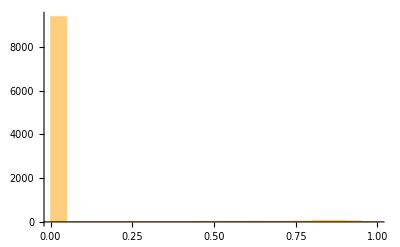

```mathematica
Histogram[subset]
```

```mathematica
Min[Cases[subset,x_/;x>0]]
```

0.00622887

```mathematica
Max[Cases[subset,x_/;x>0]]
```

0.990678

## Conversion

I see. So, ocean is highly negative. We want pixels that are greater than 0 and less than 1.

Conversion to latitude / longitude:
* Latitude: 3480 rows. Goes from -60 to 85. Convert 3480 units to 145 units. Conversion factor of 24.
* Longitude: 8640 columns. Goes from -180 to 180. Convert 8640 units to 360 units. Conversion factor of 24.

```mathematica
indexToLat[index_]:=-60+index/24.
```

```mathematica
indexToLong[index_]:=-180+index/24.
```

```mathematica
latToIndex[lat_]:=Round[1440+lat*24]
```

```mathematica
longToIndex[long_]:=Round[4320+long*24]
```

## Cities

```mathematica
cities=CityData[{All,"Brazil"}];
```

```mathematica
Length[cities]
```

2346

```mathematica
lats=Map[CityData[#,"Latitude"]&,cities];
```

```mathematica
longs=Map[CityData[#,"Longitude"]&,cities];
```

```mathematica
pops=Map[CityData[#,"Population"]&,cities];
```

```mathematica
missingPos=Union[Flatten[{Position[lats,Missing][[All,1]],Position[longs,Missing][[All,1]],Position[pops,Missing][[All,1]]}]];
```

```mathematica
lats=Delete[lats,Map[{#}&,missingPos]];
```

```mathematica
longs=Delete[longs,Map[{#}&,missingPos]];
```

```mathematica
pops=Delete[pops,Map[{#}&,missingPos]];
```

```mathematica
lats=Map[QuantityMagnitude[#]&,lats];
```

```mathematica
longs=Map[QuantityMagnitude[#]&,longs];
```

```mathematica
pops=Map[QuantityMagnitude[#]&,pops];
```

```mathematica
getSuitability[lat_,long_]:=Module[{latIndex,longIndex,value},
latIndex=latToIndex[lat];
longIndex=longToIndex[long];
value=If[latIndex>0&&longIndex>0&&latIndex<3480&&longIndex<8640,
geo[[latIndex,longIndex]],
Null
];
If[value>0,value,Null]
]
```

```mathematica
getSuitability[lat_,long_]:=Module[{latIndex,longIndex,value},
latIndex=latToIndex[lat];
longIndex=longToIndex[long];
value=If[latIndex>0&&longIndex>0&&latIndex<3480&&longIndex<8640,
geo[[latIndex,longIndex]],
Null
];
If[value>0,value,0]
]
```

```mathematica
subsetData=DeleteCases[MapThread[With[{suitability=getSuitability[#1,#2]},If[suitability===Null,Null,{#1,#2,#3,suitability}]]&,{lats,longs,pops}],Null];
```

```mathematica
dataForCountry[country_]:=Module[{cities,lats,longs,pops,weights,missingPos},
cities=CityData[{All,country}];
lats=Map[CityData[#,"Latitude"]&,cities];
longs=Map[CityData[#,"Longitude"]&,cities];
pops=Map[CityData[#,"Population"]&,cities];
missingPos=Union[Flatten[{Position[lats,Missing][[All,1]],Position[longs,Missing][[All,1]],Position[pops,Missing][[All,1]]}]];
lats=Delete[lats,Map[{#}&,missingPos]];
longs=Delete[longs,Map[{#}&,missingPos]];
pops=Delete[pops,Map[{#}&,missingPos]];
lats=Map[QuantityMagnitude[#]&,lats];
longs=Map[QuantityMagnitude[#]&,longs];
pops=Map[QuantityMagnitude[#]&,pops];
DeleteCases[MapThread[With[{suitability=getSuitability[#1,#2]},If[suitability===Null,Null,{#1,#2,#3,suitability}]]&,{lats,longs,pops}],Null]
]
```

```mathematica
baseColorFunction[t_]:=Blend[{GrayLevel[0.99],Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

```mathematica
(*baseColorFunction[t_]:=ColorData["TemperatureMap"][t]*)
```

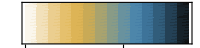

```mathematica
DensityPlot[x,{x,0,1},{y,0,1},ColorFunction->baseColorFunction,ColorFunctionScaling->True,AspectRatio->0.1,PlotRangePadding->0,FrameTicks->{{None,None},{Automatic,None}}, ImageSize->200]
```

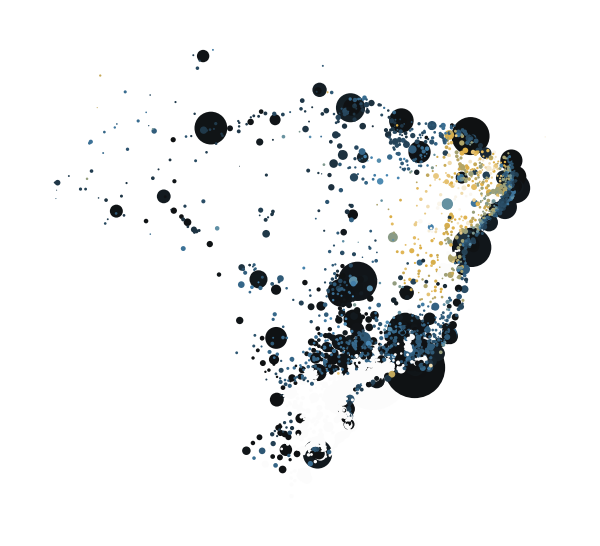

```mathematica
map=Graphics[Map[{baseColorFunction[#[[4]]],PointSize[0.00003*Sqrt[#[[3]]]],Point[{#[[2]],#[[1]]}]}&,dataForCountry["Brazil"]],ImageSize->600]
```

```mathematica
Export["brazil.png",map,"PNG",ImageResolution->100]
```

brazil.png

## Countries

```mathematica
countries=Map[CanonicalName,Join[CountryData["NorthAmerica"],CountryData["SouthAmerica"]]]
```

{Anguilla,AntiguaBarbuda,Aruba,Bahamas,Barbados,Belize,Bermuda,BritishVirginIslands,Canada,CaymanIslands,CostaRica,Cuba,Curacao,Dominica,DominicanRepublic,ElSalvador,Greenland,Grenada,Guadeloupe,Guatemala,Haiti,Honduras,Jamaica,Martinique,Mexico,Montserrat,Nicaragua,Panama,PuertoRico,SaintKittsNevis,SaintLucia,SaintPierreMiquelon,SaintVincentGrenadines,SintMaarten,TrinidadTobago,TurksCaicosIslands,UnitedStates,UnitedStatesVirginIslands,Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,FalklandIslands,FrenchGuiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
collectedData=Map[dataForCountry,countries];
```

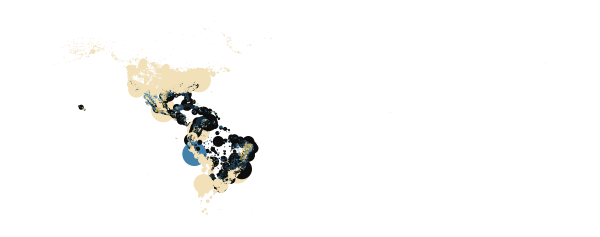

```mathematica
map=Graphics[Map[{baseColorFunction[#[[4]]+0.1],PointSize[0.00001*Sqrt[#[[3]]]],Point[{#[[2]],#[[1]]}]}&,Flatten[collectedData,1]],ImageSize->600]
```

```mathematica
Export["americas-suitability.png",map,"PNG",ImageResolution->1200]
```

americas-suitability.png

```mathematica
singleCountry=collectedData[[1]]
```

{{18.23,-63.05,1526,0.0285734},{18.22,-63.05,1378,0.0285734},{18.22,-63.05,1225,0.0285734},{18.21,-63.04,1161,0.0285734},{18.26,-63.01,910,0.0285734},{18.2,-63.07,871,0.0285734},{18.18,-63.09,819,0.0346337},{18.17,-63.15,799,0},{18.2,-63.03,700,0.0285734},{18.23,-63.,633,0.0285734},{18.21,-63.08,454,0.0285734},{18.2,-63.09,326,0.0285734}}

```mathematica
weights=N[singleCountry[[All,3]]/Total[singleCountry[[All,3]]]]
```

{0.14127,0.127569,0.113405,0.10748,0.0842437,0.0806332,0.0758193,0.0739678,0.0648028,0.0586003,0.0420293,0.0301796}

```mathematica
Total[singleCountry[[All,4]]*weights]
```

0.0269194

```mathematica
averageValueForCountrySubset[subset_]:=Module[{weights},
weights=N[subset[[All,3]]/Total[subset[[All,3]]]];
Total[subset[[All,4]]*weights]
]
```

```mathematica
averageValueForCountrySubset[singleCountry]
```

0.0269194

```mathematica
averageValues=Map[averageValueForCountrySubset,collectedData]
```

{0.0269194,0.540756,0.546932,0.839719,0.98156,0.804038,0.0997563,0.550058,0.,0.305685,0.864093,0.878205,0.643753,0.650753,0.895872,0.950706,0.,0.897331,0.80957,0.450047,0.926644,0.863965,0.898899,0.869583,0.306216,0.799962,0.892162,0.921726,0.952847,0.199814,0.943526,0.,0.720203,0.688759,0.968913,0.121798,0.208427,0.535347,0.370595,0.380693,0.649573,0.,0.613871,0.559238,0.,0.893181,0.791691,0.957578,0.399651,0.961076,0.0497532,0.876832}

```mathematica
Export["americas-suitability.tsv",MapThread[{#1,#2}&,{countries,averageValues}],"Table"]
```

americas-suitability.tsv